```mathematica
(*3a*)
```

```mathematica
D[x*(r-Exp[x]),x]//FullSimplify
```

r-ⅇ^x (1+x)

```mathematica
Solve[r==r*(1+Log[r]),r]
```

{{r→1}}

```mathematica
(*r=0*)
```

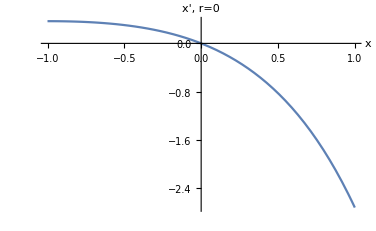

```mathematica
Plot[x*(0-Exp[x]),{x,-1,1},AxesLabel->{x,"x', r=0"}]
```

```mathematica
(*r=1*)
```

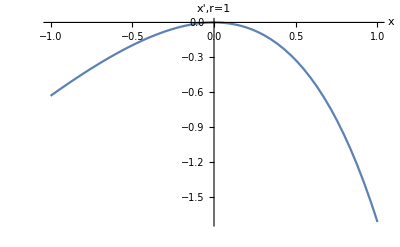

```mathematica
Plot[x*(1-Exp[x]),{x,-1,1},AxesLabel->{x,"x',r=1"}]
```

```mathematica
(*r=2*)
```

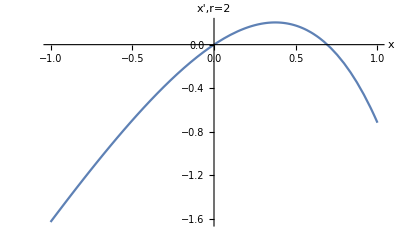

```mathematica
Plot[x*(2-Exp[x]),{x,-1,1},AxesLabel->{x,"x',r=2"}]
```

```mathematica
(*bifurcation diagram*)
```

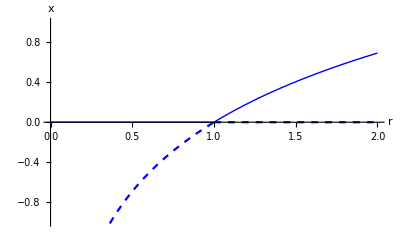

```mathematica
a=Plot[0,{r,0,1},PlotStyle->{Thick,Thick,Blue},AxesLabel->{r,x}];
b=Plot[Log[r],{r,0,1},PlotStyle->{Dashed,Blue},AxesLabel->{r,x}];
c=Plot[0,{r,1,2},PlotStyle->{Dashed,Blue},AxesLabel->{r,x}];
d=Plot[Log[r],{r,1,2},PlotStyle->{Thick,Blue},AxesLabel->{r,x}];
Show[a,b,c,d,PlotRange->{{0,2},{-1,1}}]
```

```mathematica
(*3b*)
```

```mathematica
D[r+x-Log[1+x],x]//FullSimplify
```

x/(1+x)

```mathematica
(*r=-1*)
```

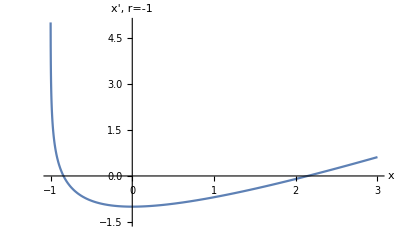

```mathematica
Plot[-1+x-Log[1+x],{x,-1.5,3},AxesLabel->{x,"x', r=-1"},PlotRange->{-1.5,5}]
```

```mathematica
(*r=0*)
```

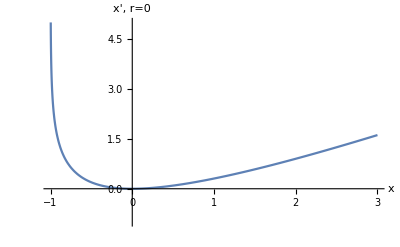

```mathematica
Plot[0+x-Log[1+x],{x,-1.5,3},AxesLabel->{x,"x', r=0"},PlotRange->{-1,5}]
```

```mathematica
(*r=1*)
```

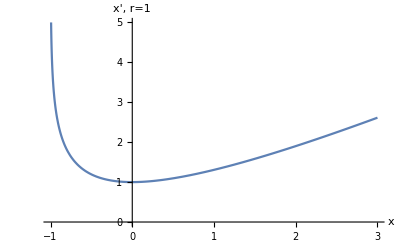

```mathematica
Plot[1+x-Log[1+x],{x,-1.5,3},AxesLabel->{x,"x', r=1"},PlotRange->{0,5}]
```

```mathematica
(*bifurcation diagram*)
```

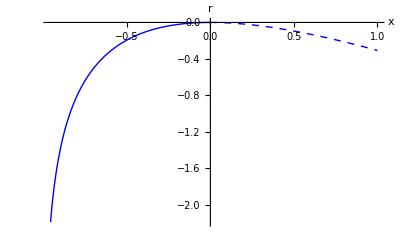

```mathematica
a=Plot[-x+Log[1+x],{x,0,1},PlotStyle->{Dashed,Thick,Blue},AxesLabel->{x,"r"}];
b=Plot[-x+Log[1+x],{x,-1,0},PlotStyle->{Thick,Thick,Blue},AxesLabel->{x,"r"}];
Show[a,b,PlotRange->{0.25,-2}]
```

```mathematica
(*3c*)
```

```mathematica
D[x+Tanh[r*x],x]
```

1+r Sech[r x]^2

```mathematica
FindRoot[{-x==Tanh[r*x],1+r*Sech[r*x]^2==0},{{r,0},{x,0}}]
```

{r→-1.,x→0.}

```mathematica
(*r=-3*)
```

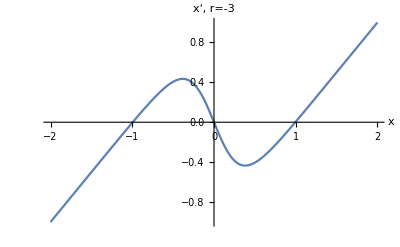

```mathematica
Plot[x+Tanh[-3*x],{x,-2,2},AxesLabel->{x,"x', r=-3"},PlotRange->Full]
```

```mathematica
(*r=-1*)
```

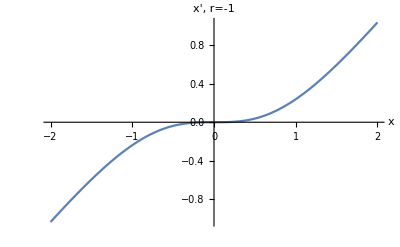

```mathematica
Plot[x+Tanh[-1*x],{x,-2,2},AxesLabel->{x,"x', r=-1"},PlotRange->Full]
```

```mathematica
(*r=1*)
```

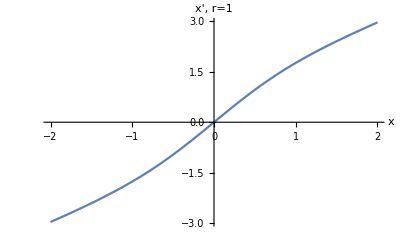

```mathematica
Plot[x+Tanh[1*x],{x,-2,2},AxesLabel->{x,"x', r=1"},PlotRange->Full]
```

```mathematica
(*bifurcation diagram*)
```

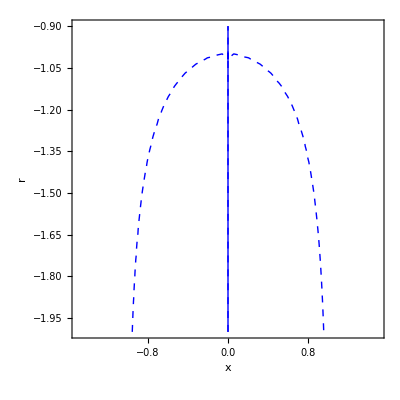

```mathematica
a=ContourPlot[-x==Tanh[r*x],{x,-0.001,0.001},{r,-2,-0.9},ContourStyle->{Thick,Thick,Blue},FrameLabel->{x,r},PlotRange->{{-1.5,1.5},{-2,-0.9}}];
b=ContourPlot[-x==Tanh[r*x],{x,-1.5,1.5},{r,-2,-0.9},ContourStyle->{Dashed,Thick,Blue},FrameLabel->{x,r}];
Show[a,b]
```